## Near the Bang (a=0)

(-6 a^2+a^4 k^2 (3+4/m^2)+(4 k^2)/m^2+a^6 (-2+3 m^2)) ψt[a]+2 a (a^6+((1+a^4) k^2)/m^2) ψt'[a]+a^4 (1+a^4) ψt''[a]==0

DSolve::bvsing: Unable to resolve some of the arbitrary constants in the general solution using the given boundary conditions. It is possible that some of the conditions have been specified at a singular point for the equation.

{{ψt[a]→a^3 C[2] Hypergeometric2F1[7/8-1/8 √3 √(3-4 m^2),7/8+1/8 √3 √(3-4 m^2),9/4,-a^4]}}

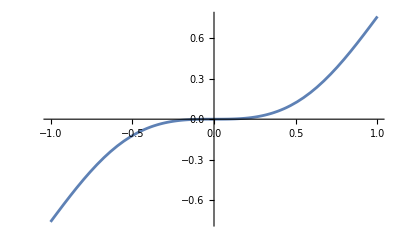

```mathematica
(*Solve the equation with k=0*)
Clear[equation,a,ψt]
equation = a^4 (1+a^4)ψt''[a]+2a(a^6+(1+a^4)k^2/m^2)ψt'[a]+(4 k^2/m^2-6 a^2+k^2(4/m^2+3) a^4+(3 m^2-2)a^6) ψt[a]==0
solution= DSolve[{equation/.{k->0}, ψt[0]==0,ψt'[0]==0},ψt[a],a]
Plot[Evaluate[ ψt[a]/.solution/. {C[2]->1,m->1}],{a,-1,1},PlotRange->All]
```

```mathematica
(* Solve the equation by Taylor expansion *)
Clear[a,ψt ]
(* Define the power series *)
ψt=With[{nmax=3},Sum[psit[3+4n] a^(3+4n),{n,0,nmax}]+O[a]^(3+4nmax+1)];
eqψt=a^4 (1+a^4)Evaluate[D[ψt,{a,2}]]+2a(a^6+(1+a^4)k^2/m^2)Evaluate[D[ψt,a]]+(4 k^2/m^2-6 a^2+k^2(4/m^2+3) a^4+(3 m^2-2)a^6) ψt==0;

(* Expand the differential euqations by power series *)
eqs=LogicalExpand[eqψt/.{k->0}]

Simplify[Solve[eqs,{psit[7],psit[11]}]]
```

12 psit[3]+(-2+3 m^2) psit[3]+36 psit[7]==0&&56 psit[7]+(-2+3 m^2) psit[7]+104 psit[11]==0

{{psit[7]→-1/36 (10+3 m^2) psit[3],psit[11]→((180+64 m^2+3 m^4) psit[3])/1248}}

## Near the end of the universe

```mathematica
(*Solve the equation near the end of the universe*)
DSolve[{a^2 ψt''[a]+2a ψt'[a]+(3 m^2-2) ψt[a]==0},ψt[a],a]
```

{{ψt[a]→a^(1/2 √(-2+3 m^2) (-1/(√(-2+3 m^2))-√(-4+1/(-2+3 m^2)))) C[1]+a^(1/2 √(-2+3 m^2) (-1/(√(-2+3 m^2))+√(-4+1/(-2+3 m^2)))) C[2]}}

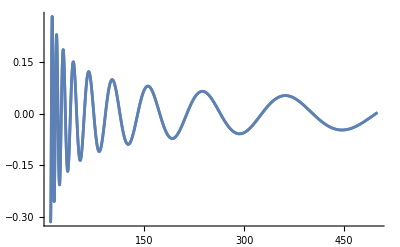

```mathematica
Plot [{Re[a^(1/2 √(-2+3 m^2) (-1/(√(-2+3 m^2))-√(-4+1/(-2+3 m^2))))] ,Re[a^(1/2 √(-2+3 m^2) (-1/(√(-2+3 m^2))+√(-4+1/(-2+3 m^2)))) ]}/.{m->10√3/2 },{a,10,500}]
```

```mathematica
{Abs[a^(1/2 √(-2+3 m^2) (-1/(√(-2+3 m^2))-√(-4+1/(-2+3 m^2))))] ,Abs[a^(1/2 √(-2+3 m^2) (-1/(√(-2+3 m^2))+√(-4+1/(-2+3 m^2)))) ]}/.{m->0.5√3/2 ,a->∞}
```

{∞,0}

```mathematica
(* Transform the equation to w.r.t s=1/a*)
Clear[equation,a,s,ψt,y]
equation = a^4 (1+a^4)ψt''[a]+2a(a^6+(1+a^4)k^2/m^2)ψt'[a]+(4 k^2/m^2-6 a^2+k^2(4/m^2+3) a^4+(3 m^2-2)a^6) ψt[a]==0
(*Variable substitution*)
substitutionRules={a->1/s,ψt'[a]->-s^2 y'[s],ψt''[a]->2 s^3 y'[s]+s^4 y''[s],ψt[a]->y[s]};
(*Apply the substitution*)
transformedEquation=equation/. substitutionRules;
(*Simplify the equation*)
simplifiedEquation=Simplify[ transformedEquation];
(*Display the transformed equation*)
simplifiedEquation
DSolve[{simplifiedEquation, y[0]==0,y'[0]==0}/.{k->0},y[s],s]
```

(-6 a^2+a^4 k^2 (3+4/m^2)+(4 k^2)/m^2+a^6 (-2+3 m^2)) ψt[a]+2 a (a^6+((1+a^4) k^2)/m^2) ψt'[a]+a^4 (1+a^4) ψt''[a]==0

((3 m^4+m^2 (-2+3 k^2 s^2-6 s^4)+4 k^2 s^2 (1+s^4)) y[s]+s^2 (-2 (-m^2 s^3+k^2 (s+s^5)) y'[s]+m^2 (1+s^4) y''[s]))/(m s)==0

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{y[s]→((m^2-2 k^2 s^2) C[1])/m^2+((m^2-2 k^2 s^2) C[2] ((2 ⅇ^((k^2 s^2)/m^2) m s)/(m^2-2 k^2 s^2)+(√π Erfi[(k s)/m])/k))/(4 m^5)}}

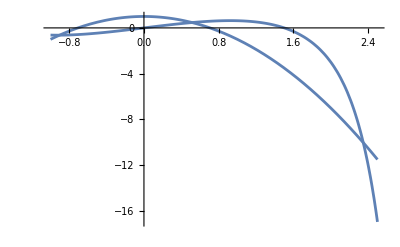

```mathematica
(* Solve the equation when s -> ∞ *)
SinfinityEq=4 y[s]-2s y'[s]+m^2 /k^2 y''[s]==0;
solution=DSolve[{SinfinityEq},y[s],s]
(*Plot[{Evaluate[ y[s]/.solution/. {C[2]->0,C[1]->1}],Evaluate[ y[s]/.solution/. {C[2]->1,C[1]->0}]}/.{k->1,m->1},{s,-1,2.5},PlotRange->All]*)
Plot[{Evaluate[ y[s]/.solution/. {C[2]->1,C[1]->0}],Evaluate[ y[s]/.solution/. {C[2]->0,C[1]->1}]}/.{k->1,m->1},{s,-1,2.5},PlotRange->All]
```

```mathematica
(* Solve the equation by Taylor expansion at s=0 *)
Clear[s,ψt,eqψt,eqs ]
(* Define the power series *)
ψt=With[{nmax=10},Sum[psit[n] s^n,{n,0,nmax}]+O[s]^(nmax+1)];
eqψt=(3 m^4+m^2 (-2+3 k^2 s^2-6 s^4)+4 k^2 s^2 (1+s^4))ψt+s^2 (-2 (-m^2 s^3+k^2 (s+s^5)) Evaluate[D[ψt,s]]+m^2 (1+s^4) Evaluate[D[ψt,{s,2}]])==0;

(* Expand the differential euqations by power series *)
eqs=LogicalExpand[eqψt/.{m->Sqrt[2/3]}]
```

6 k^2 psit[0]+(4 psit[2])/3==0&&4 k^2 psit[1]+4 psit[3]==0&&-4 psit[0]+2 k^2 psit[2]+8 psit[4]==0&&-(8 psit[1])/3+(40 psit[5])/3==0&&4 k^2 psit[0]-2 k^2 psit[4]+20 psit[6]==0&&2 k^2 psit[1]+4 psit[3]-4 k^2 psit[5]+28 psit[7]==0&&(28 psit[4])/3-6 k^2 psit[6]+(112 psit[8])/3==0&&-2 k^2 psit[3]+16 psit[5]-8 k^2 psit[7]+48 psit[9]==0&&-4 k^2 psit[4]+24 psit[6]-10 k^2 psit[8]+60 psit[10]==0